Lo que no se vio en el libro

Hay mucho más material en Wolfram Language de lo que se ha presentado en este libro. A continuación, se verá una muestra de algunos de los muchos temas y áreas que no se han abordado.

#### Construcción de interfaces de usuario

Forme una interfaz con pestañas:

```mathematica
TabView[Table[ListPlot[Range[20]^n],{n,5}]]
```

12345

Las interfaces de usuario son simplemente otro tipo de expresión simbólica. Forme una rejilla de deslizadores:

```mathematica
Grid[Table[Slider[ ],4,3]]
```

|  | 
 |  | 
 |  | 
 |  |

### Visualización de funciones

Grafique una función:

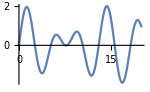

```mathematica
Plot[Sin[x]+Sin[Sqrt[2] x],{x,0,20}]
```

Un gráfico de contornos en 3D:

```mathematica
ContourPlot3D[x^3+y^2-z^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

#### Computación matemática

Realice cálculos simbólicos, con x como variable algebraica:

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

Obtenga la solución de ecuaciones en forma simbólica:

```mathematica
Solve[x^3-2x+1==0,x]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

Trabaje simbólicamente con temas del cálculo:

```mathematica
Integrate[Sqrt[x+Sqrt[x]],x]
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

Muestre resultados en la forma matemática tradicional:

```mathematica
Integrate[AiryAi[x],x]//TraditionalForm
```

-(x (3^(1/3) x (2/3)^2 _1 F_2(2/3;4/3,5/3;x^3/9)-3 1/3 5/3 _1 F_2(1/3;2/3,4/3;x^3/9)))/(9 3^(2/3) 2/3 4/3 5/3)

Use notación 2D en las entradas:

```mathematica
∑_(i=0)^n (Binomial[n,i] i!)/((n+1+i)!)
```

(√π)/(2 (1/2 (1+2 n))!)

#### Cálculos numéricos

Minimice una función al interior de una bola esférica:

```mathematica
NMinimize[{x^4+y^4-z/(x+1),y>0},{x,y,z}∈Ball[ ]]
```

{-7.34516,{x→-0.971029,y→0.0139884,z→0.238555}}

Resuelva una ecuación diferencial para obtener una función aproximada:

```mathematica
NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

Muestre el gráfico con la función aproximada:

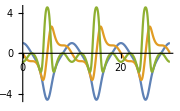

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.%],{x,0,30}]
```

#### Geometría

El área de un disco (un círculo relleno) de radio r:

```mathematica
Area[Disk[{0,0},r]]
```

π r^2

Obtenga una forma geométrica mediante un proceso de “envoltura y contracción” alrededor de 100 puntos aleatorios en 3D:

```mathematica
ConvexHullMesh[RandomReal[1,{100,3}]]
```

-Graphics-

#### Algoritmos

Encuentre la trayectoria más corta a través de las capitales de Europa (problema del viajante):

```mathematica
With[{c=LinguisticAssistant},GeoListPlot[c[[Last@FindShortestTour[c]]],Joined->True]]
```

-Graphics-

Factorización de un entero grande:

```mathematica
FactorInteger[2^255-1]
```

{{7,1},{31,1},{103,1},{151,1},{2143,1},{11119,1},{106591,1},{131071,1},{949111,1},{9520972806333758431,1},{5702451577639775545838643151,1}}

#### Lógica

Haga una tabla de verdad:

```mathematica
BooleanTable[p||q&&(p||!q),{p},{q}]//Grid
```

True | True
False | False

Encuentre una representación mínima de una función Booleana:

```mathematica
BooleanMinimize[BooleanCountingFunction[{2,3},{a,b,c,d}]]//TraditionalForm
```

(a∧b∧¬d)∨(a∧¬b∧c)∨(a∧¬c∧d)∨(¬a∧b∧d)∨(b∧c∧¬d)∨(¬b∧c∧d)

#### El universo computacional

Ejecute mi ejemplo favorito de un programa muy simple con un comportamiento muy complejo:

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},200]]
```

-Graphics-

RulePlot muestra la regla subyacente:

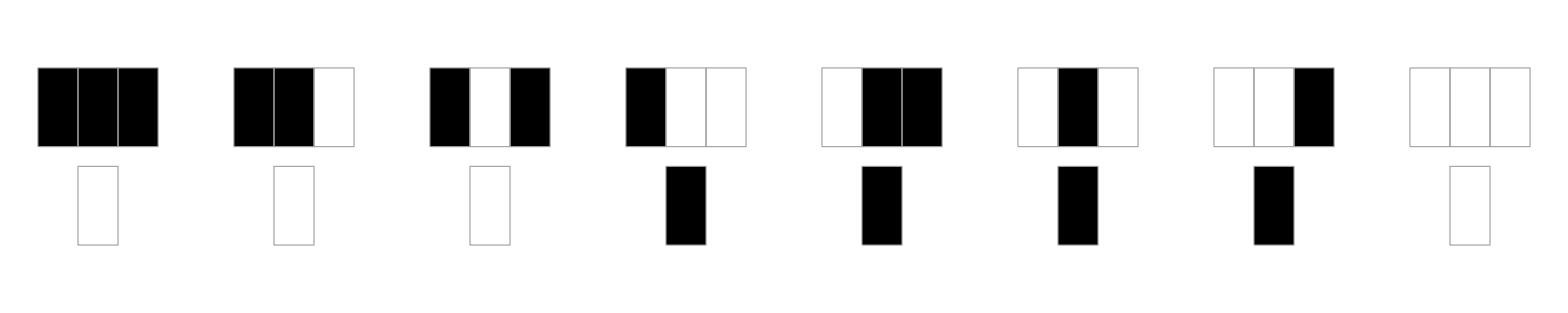

```mathematica
RulePlot[CellularAutomaton[30]]
```

#### Construcción de APIs

Active en la red una API simple que encuentre la distancia desde una ubicación especificada:

```mathematica
CloudDeploy[APIFunction[{"loc" -> "Location"}, GeoDistance[#loc, Here] &]]
```

CloudObject[]

Cree un código embebible para un programa externo en Java que llame a esa API:

```mathematica
EmbedCode[%,"Java"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Java:
Code
 | Copy to Clipboard
import java.net.URL;
import java.net.HttpURLConnection;
import java.net.URLEncoder;
import java.io.InputStream;
import java.io.BufferedReader;
import java.io.InputStreamReader;
import java.io.DataOutputStream;
import java.io.IOException;

public class WolframCloudCall {

    public static String call(String loc) throws IOException {

        URL _url = new URL("http://www.wolframcloud.com/objects/09302cdc-4d52-457e-86ae-b834bd9717ae");
        HttpURLConnection _conn = (HttpURLConnection) _url.openConnection();
        _conn.setRequestMethod("POST");
        _conn.setDoOutput(true);
        _conn.setDoInput(true);
        _conn.setUseCaches(false);
        _conn.setAllowUserInteraction(false);
        _conn.setRequestProperty("Content-Type", "application/x-www-form-urlencoded; charset=utf-8");
        _conn.setRequestProperty("User-Agent", "EmbedCode-Java/1.0");
        DataOutputStream _out = new DataOutputStream(_conn.getOutputStream());

        _out.writeBytes("loc");
        _out.writeBytes("=");
        _out.writeBytes(URLEncoder.encode("" + loc, "UTF-8"));
        _out.writeBytes("&");

        _out.close();

        if (_conn.getResponseCode() != 200) {
            throw new IOException(_conn.getResponseMessage());
        }
        
        BufferedReader _rdr = new BufferedReader(new InputStreamReader(_conn.getInputStream()));
        StringBuilder _sb = new StringBuilder();
        String _line;
        while ((_line = _rdr.readLine()) != null) {
            _sb.append(_line);
        }
        _rdr.close();
        _conn.disconnect();
        return _sb.toString();
    }
}

#### Generación de documentos

Los documentos son expresiones simbólicas, al igual que cualquier otra cosa:

```mathematica
DocumentNotebook[{Style["A Circle","Section"],Style["How to make a circle"],Graphics[Circle[ ]]}]
```

A Circle
How to make a circle
-Graphics-

#### Control de la evaluación

Mantenga una expresión sin evaluarla:

```mathematica
Hold[2+2==4]
```

Hold[2+2==4]

Desbloquee la evaluación:

```mathematica
ReleaseHold[%]
```

True

#### Operaciones en el nivel del sistema

Ejecute un proceso externo (¡no está permitido hacer esto en la nube!):

```mathematica
RunProcess["ps","StandardOutput"]
```

PID TTY           TIME CMD
  374 ttys000    0:00.03 -tcsh
40192 ttys000    0:00.66 ssh pi
60521 ttys001    0:00.03 -tcsh

Encripte algo:

```mathematica
Encrypt["sEcreTkey","Read this if you can!"]
```

EncryptedObject[<|Data -> ByteArray[<32>], InitializationVector -> ByteArray[<16>], OriginalForm -> String|>]

#### Computación en paralelo

Estoy trabajando en un equipo con 12 procesadores:

```mathematica
$ProcessorCount
```

12

Compruebe la condición de primalidad secuencialmente, en una sucesión de (grandes) números, dando el tiempo utilizado para ello:

```mathematica
Table[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{4.15402,<|True→18,False→482|>}

Si lo anterior se realiza en paralelo, el tiempo utilizado es considerablemente menor:

```mathematica
ParallelTable[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{0.572106,<|True→18,False→482|>}